## Solution CP6: Systems of linear recurrence equations

Use Mathematica to verify your answers of the pen and paper practical.

As usual, we first clear the memory of Mathematica:

```mathematica
Quit[]
```

## Solving recurrence equations with Mathematica

In Mathematica, the command RSolveValue[] is used for solving (systems of) recurrence equations. However, you will find not all systems can be solved this way; in such cases, you need to apply the method outlined in the manual and lectures, and solve the equations manually. Of course you can still use Mathematica, e.g. to calculate derivatives and to plot the solutions............ Also check out the command RecurrenceTable[] that enables you to iterate a first- or second-order recurrence equation, or a system of recurrence equations.

### Exercise 6-1

Consider the second-order recurrence equations z(t+2)=1/2 z(t+1)+1/2 z(t) and z(t+2)=2z(t+1)-2z(t).

(a) Solve both equations for z(0)=1 and z(1)=2.5

```mathematica
eq1=z[t+2]==0.5*z[t+1]+0.5*z[t]
solEQ1=RSolveValue[{eq1,z[0]==1,z[1]==2.5},z[t],t]
```

z[2+t]==0.5 z[t]+0.5 z[1+t]

-1. (-2.+1. (-0.5)^t)

```mathematica
eq2=z[t+2]==2*z[t+1]-2*z[t]
solEQ2=RSolveValue[{eq2,z[0]==1,z[1]==2.5},z[t],t]//ComplexExpand
```

z[2+t]==-2 z[t]+2 z[1+t]

(0.+0. ⅈ)+1. 2^(t/2) Cos[(π t)/4]+1.5 2^(t/2) Sin[(π t)/4]

(b) Calculate in both cases the values at time t=5.

```mathematica
solEQ1/.t->5
solEQ2/.t->5
```

2.03125

-10.-8.88178×10^-16 ⅈ

(c) Plot the solution for both cases. What can you conclude about its behaviour over time?

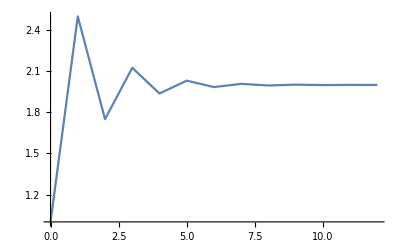

```mathematica
DiscretePlot[{solEQ1},{t,0,12},Joined->True,Filling->None,PlotRange->All]
DiscretePlot[{solEQ2},{t,0,12},Joined->True,Filling->None,PlotRange->All]
```

The system will oscillate in the beginning but will converge to the equilibrium value 2 over time.

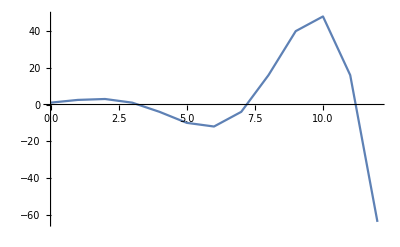

The system will oscillate in the beginning but will diverge to -∞ over time.

### Exercise 6-2

Consider two systems of recurrence equations: 
(1)   x(t+1)=3x(t)-2y(t), y(t+1)=2x(t)-2y(t)
(2)   x(t+1)=1/2 x(t)-y(t), y(t+1)=x(t)+1/2 y(t)

(a)  Solve both systems for initial values x(0)=y(0)=1

```mathematica
eqX1=x[t+1]==3*x[t]-2*y[t]
eqY1=y[t+1]==2*x[t]-2*y[t]
sys1={eqX1,eqY1};
init1={x[0]==1,y[0]==1};
{sol1,sol2}=RSolveValue[{sys1,init1},{x[t],y[t]},t]
```

x[1+t]==3 x[t]-2 y[t]

y[1+t]==2 x[t]-2 y[t]

{1/3 ((-1)^t+2^(1+t)),1/3 (2 (-1)^t+2^t)}

```mathematica
eqX2=x[t+1]==(1/2)*x[t]-y[t]
eqY2=y[t+1]==x[t]+(1/2)*y[t]
sys2={eqX2,eqY2};
init2={x[0]==1,y[0]==1};
{sol3,sol4}=RSolveValue[{sys2,init2},{x[t],y[t]},t]
{sol3,sol4}=RSolveValue[{sys2,init2},{x[t],y[t]},t]//ComplexExpand//Simplify (* We see complex solutions so use //ComplexExpand//Simplify to see things in terms of sine and cosine*)
```

x[1+t]==x[t]/2-y[t]

y[1+t]==x[t]+y[t]/2

{(1+ⅈ) 2^(-1-t) (-ⅈ (1-2 ⅈ)^t+(1+2 ⅈ)^t),(1+ⅈ) 2^(-1-t) ((1-2 ⅈ)^t-ⅈ (1+2 ⅈ)^t)}

{2^-t 5^(t/2) (Cos[t ArcTan[2]]-Sin[t ArcTan[2]]),2^-t 5^(t/2) (Cos[t ArcTan[2]]+Sin[t ArcTan[2]])}

(b) Calculate x(5) and y(5)  for both sets of solutions

```mathematica
sol1/.t->5
sol2/.t->5
```

21

10

```mathematica
N[sol3/.t->5]
N[sol4/.t->5]
```

2.46875

0.09375

(c) Plot the solutions.for both systems

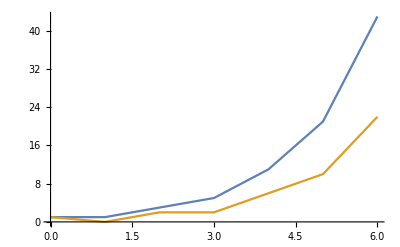

```mathematica
DiscretePlot[{sol1,sol2},{t,0,6},Joined->True,Filling->None]
```

Over time, the system will diverge monotonously.

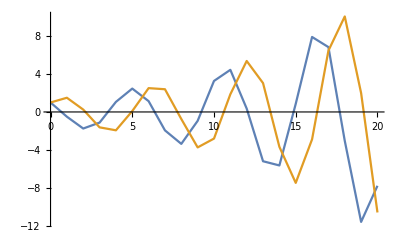

```mathematica
DiscretePlot[{sol3,sol4},{t,0,20},Joined->True,Filling->None]
```

Over time, the system will oscillate with increasing amplitude.

### Exercise 6-3

Consider the recurrence equations:
z(t+1)=0.9z(t)+0.5r(t)
r(t+1)=0.1z(t)+0.5r(t)

(a) Solve this system of recurrence equations and plot the solutions

```mathematica
eqZ=z[t+1]==0.9*z[t]+0.5*r[t]
eqR=r[t+1]==0.1*z[t]+0.5*r[t]
sys={eqZ,eqR};
init={z[0]==1,r[0]==0};
{solZ,solR}=RSolveValue[{sys,init},{z[t],r[t]},t]
```

z[1+t]==0.5 r[t]+0.9 z[t]

r[1+t]==0.5 r[t]+0.1 z[t]

{0.166667 (5.+1. 0.4^t),-0.166667 (-1.+1. 0.4^t)}

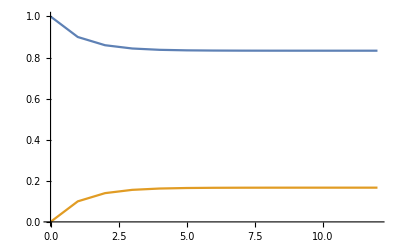

```mathematica
DiscretePlot[{solZ,solR},{t,0,12.},Joined->True,Filling->None]
```

(b) Implement the system from (a) as a second-order recurrence equation and solve it; plot the solution.

z[t + 1] == 0.9*z[t] + 0.5*r[t] can  be  rewritten  as  r[t] == 2*(z[t + 1] - 0.9*z[t])
 Applying  it  to  t + 1  leads  to  z[t + 2] == 0.9*z[t + 1] + 0.5*r[t + 1]
 We  can  substitute  the  second equation : z[t + 2] == 0.9*z[t + 1] + 0.5*(0.1*z[t]+0.5*r[t])
 And  then  we  can  substitute  our  equation  above  for  r[t] : z[t + 2] == 0.9*z[t + 1] + 0.5*(0.1*z[t]+0.5*2*(z[t+1]-0.9*z[t]))
=1.4  z[t + 1] - 0.4  z[t]

```mathematica
eqz2=z[t+2]==1.4z[t+1]-0.4z[t]
```

z[2+t]==-0.4 z[t]+1.4 z[1+t]

0.166667 (5.+1. 0.4^t)

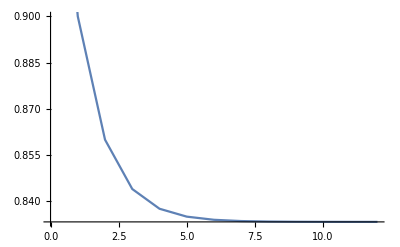

```mathematica
solution=RSolveValue[{eqz2,z[0]==1,z[1]==0.9},z[t],t]
DiscretePlot[{solution},{t,0,12},Joined->True,Filling->None]
```

(c) Calculate the probability of nice weather next Saturday, i.e., z(4)

```mathematica
solution/.t->4
```

0.8376